## Naloga 1

Obravnavaj met žogice iz višine H v smeri vektorja v0 = {v0x, v0y}.Upoštevaj gravitacijski pospešek g = 9.81 m/s2.Pomagaj si z naslednjimi koraki :

```mathematica
v0={10,3};
GG=9.81;
H=10;
a ={0,-GG};
x0 ={0,H};
v[t_] := {v0 [[1]],v0[[2]] - GG*t}
v[t_] := v0 + a *t
v[1]
```

{10,-6.81}

```mathematica
X[t_] := x0 + v0 * t + (a * t^2)/2
X[1]
```

{10,8.095}

```mathematica
SlikaTocke[t_] :={PointSize[0.03],Point[X[t]]}

Manipulate[Graphics[SlikaTocke[t],Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,1.766035}]
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}
```

```mathematica
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}

Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,1.076}]
```

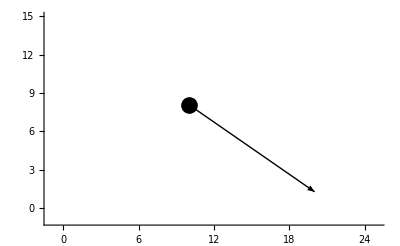

```mathematica
Graphics[{SlikaTocke[1] ,SlikaVektorja[1]},Axes->True, PlotRange->{{-1,25},{-1,15}}, AspectRatio->Automatic]
```

```mathematica
Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{-1,25},{-5,15}}, AspectRatio->Automatic],{t,0,5}]
```

```mathematica
dolzinaHitrosti = Sqrt[v0[[1]]^2+v0[[2]]^2]
sinusKota = N[v0[[2]] / dolzinaHitrosti]
```

√109

0.287348

```mathematica
najvisjaTocka = dolzinaHitrosti^2 * sinusKota^2/(2 * GG) + H
casDoNajvisjeTocke = 2 * dolzinaHitrosti * sinusKota/(GG * 2)
domet = dolzinaHitrosti^2 * Sin[2 * ArcSin[sinusKota]]/GG + H
{casLeta} = t /.  Solve[X[t][[2]] == 0 &&  t>0, t]
```

10.4587

0.30581

16.1162

{1.76604}

```mathematica
Manipulate[Graphics[{{SlikaVektorja[t],Thick}, SlikaTocke[t]}, Axes -> True, PlotRange->{{-1, Round[domet] + 2}, {-1, Round[najvisjaTocka] + 1}}, AspectRatio->1], {t,0, casLeta}]
```

```mathematica
absHitrosti=√((v[casLeta][[1]])^2  + (v[casLeta][[2]])^2)
```

17.47

## Naloga 2

Ravnino podamo v obliki Ravnina[n_, v_], kjer je n normala na ravnino in je v točka na
ravnini.Npr.ravnina, ki gre skozi točko (1, 1, 1) in je pravokotna na glavno diagonalo je r111 = Ravnina[{-1, -1, -1}, {1, 1, 1}].

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]] := Hyperplane[n,v]
```

-Graphics3D-

```mathematica
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

```mathematica
Normala[Ravnina[n_,v_]] := n
Normala[r111]
```

{-1,-1,-1}

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}]
ry = Ravnina[{0, 1, 0}, {0, 0, 0}]
rz = Ravnina[{0, 0, 1}, {0, 0, 0}]
Slika[r111]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

Hyperplane[{-1,-1,-1},{1,1,1}]

```mathematica
SlikaNormale[Ravnina[n_,v_]] := Arrow[{v,v+n}]
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeNormal}, PlotRange->{{-1, 2}, {-1,2},{-1,2}}]
Graphics3D[{Slika[r111], SlikaNormale[r111]}]
```

-Graphics3D-

-Graphics3D-

```mathematica
slikeRavnin = Map[Slika, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

## Naloga 3

Izberi si neko 3D telo in ga nariši s pomočjo točk in poligonov. Enostavni primeri so kocke, kvadri. Bolj napredni so piramide, prizme, prerezane piramide. . . Bodite izvirni in narišite nekaj lepega. Narišite tudi normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

```mathematica
AA = {0,0,0};
BB = {2,0,0};
CC = {2,2,0};
DD = {0,2,0};
EE = {1,1,2};
```

```mathematica
Slika1 =Graphics3D[Pyramid[{AA,BB,CC,DD,EE}]]
```

-Graphics3D-